```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab6\lab6

```mathematica
implicit = Import["ImplicitEulerPendulum.txt","Table"];
explicit= Import["ExplicitEulerPendulum.txt","Table"];
symmetical = Import["SymmetricalSchemePendulum.txt","Table"];
rungekutta=Import["RungeKuttaPendulum.txt","Table"];
Length@implicit
```

101

```mathematica
ListPlot[{implicit, explicit,symmetical,rungekutta},PlotLegends->{"Неявный", "Явный", "Рунге-Кутта 4 порядка"},ImageSize->600,PlotRange->{{-100,100},{-100,100}}]
```

-Graphics-

```mathematica
explicitBatched= Import["batchedtest.txt","Table"];
Length@explicitBatched
```

101000

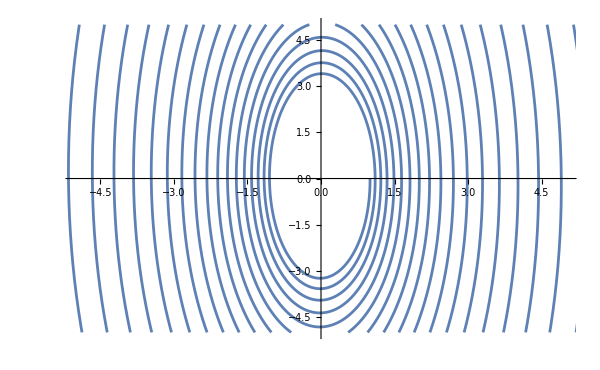

```mathematica
ListPlot[{ explicitBatched},Joined->True,ImageSize->600,PlotRange->{{-5,5},{-5,5}}]
```